# Derivation of scattering from a solid spherical shell.

```mathematica
$Assumptions:={Ri>0,Ro>0, q>0,r>0,Sin[θq]>= 0,θq> 0,θq<= π/2}
```

Here we look at a solid spherical shell with a constant scattering length density. In spherical coordinates

```mathematica
Rvec:={r Cos[θ]Sin[ϕ],r Sin[θ]Sin[ϕ],r Cos[ϕ]}
```

Here ϕ is the angle  Rvec makes with the z axis and θ is the angle the xy projection makes with the x axis. The measure with this choice of coordinates is r^2 dθ dCos[ϕ]
We can place the q vecor along any direction due to rotational symmetry, easiest direction is z

```mathematica
qvec={0,0,q}
```

{0,0,q}

```mathematica
Rvec.qvec
```

q r Cos[ϕ]

Integrating over angles gives the normalized scattering of an Infinitely thin shell of radius r.

```mathematica
Aishell=Integrate[Exp[I q r Cosθ ]/(4 π), {Cosθ ,-1,1},{ϕ,-π,π}]
```

Sin[q r]/(q r)

Some useful normalization constants for a finite with shell (Ri inner radius, Ro outer radius): surface of the unit sphere, and radial factor for calculating the volume of a sphere:

```mathematica
Normalization=Integrate[Sin[θ] r^2,{θ,0,π},{ϕ,-π,π},{r,Ri,Ro}]//Simplify
```

4/3 π (-Ri^3+Ro^3)

Kind of obvious but math works out to the volume. To get the form factor amplitude relative to the centre of the spherical shell, we integrate the interference contribution from all scatterers on a spherical surface at r:

```mathematica
Ashellcenter=Integrate[Exp[I q r Cosθ ]/Normalization r^2, {Cosθ ,-1,1},{ϕ,-π,π},{r,Ri,Ro}]//Expand
```

-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3))

```mathematica
Ashellcenter/.Ri->xi/q/.Ro->xo/q//Simplify
```

-(3 (xi Cos[xi]-xo Cos[xo]-Sin[xi]+Sin[xo]))/(xi^3-xo^3)

```mathematica
CForm[%]/.Power->pow
```

-3*pow(pow(xi,3) - pow(xo,3),-1)*(xi*Cos(xi) - xo*Cos(xo) - Sin(xi) + Sin(xo))

Which is the form factor amplitude relative to the centre of the sphere . Any pair distance between two scatterers can be stated as the convolution of two vectors connecting a scatterer to the origin . Fourier transforming the pair distance turns it into products of the Fourier transforms . Hence the form factor is just the form factor amplitude squared :

```mathematica
Fshell=Ashellcenter^2
```

(-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3)))^2

#### Guinier expansion of Form Factor

```mathematica
Series[Fshell,{q,0,3}]
Solve[Normal[%]==1-(Rg2 q^2)/3,Rg2]//Simplify
Rg2/.%[[1]]
CForm[%]/.Power->pow
```

1+(-Ri^5/(5 (Ri^3-Ro^3))+Ro^5/(5 (Ri^3-Ro^3))) q^2+O[q]^4

{{Rg2→(3 (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4))/(5 (Ri^2+Ri Ro+Ro^2))}}

(3 (Ri^4+Ri^3 Ro+Ri^2 Ro^2+Ri Ro^3+Ro^4))/(5 (Ri^2+Ri Ro+Ro^2))

(3*(Ro*pow(Ri,3) + pow(Ri,4) + pow(Ri,2)*pow(Ro,2) + Ri*pow(Ro,3) + pow(Ro,4))*
     pow(Ri*Ro + pow(Ri,2) + pow(Ro,2),-1))/5.

#### Guinier expansions of amplitudes and phase factors

Having derived Ashellcenter which is the distance from the center to any scatterer, we can convolute this with various distributed reference points, such as the inner or outer surface of the spherical shell. Convolutions turn into products when we Fourier transform. Hence the form factor amplitude of the shell relative to a random selected point on the inner or outer surface is just Ashell_outersurface = AshellcenterSin[Ro q]/(q Ro). To calculate the form factor amplitude relative to a random point on the surface we should weight the inner and outer surfaces by their respective surface area fractions.
Similarily calculating the phase factors e.g. from a random point on the inner surface to a random point on the outer surface is again the convolution of these two, which turns into the product of Aishell[Ro]Aishell[Ri]. It gets slightly more complicated for the phase factor for two points on any surface:

```mathematica
Ainner2shell:=Sin[Ri q]/(q Ri)Ashellcenter
Aouter2shell:=Sin[Ro q]/(q Ro)Ashellcenter
Asurface2shell:=((4π Ro^2 Sin[Ro q]/(q Ro)+4π Ri^2 Sin[Ri q]/(q Ri))/(4π(Ro^2+ Ri^2)))Ashellcenter
Pinner2inner:=(Sin[Ri q]/(q Ri))^2
Pouter2outer:=(Sin[Ro q]/(q Ro))^2
Pinner2outer:=Sin[Ri q]/(q Ri)Sin[Ro q]/(q Ro)
Pcenter2surface:=((4π Ro^2 Sin[Ro q]/(q Ro)+4π Ri^2 Sin[Ri q]/(q Ri))/(4π(Ro^2+ Ri^2)))
Pinner2surface:=Sin[Ri q]/(q Ri)((4π Ro^2 Sin[Ro q]/(q Ro)+4π Ri^2 Sin[Ri q]/(q Ri))/(4π(Ro^2+ Ri^2)))
Pouter2surface:=Sin[Ro q]/(q Ro)((4π Ro^2 Sin[Ro q]/(q Ro)+4π Ri^2 Sin[Ri q]/(q Ri))/(4π(Ro^2+ Ri^2)))
Psurface2surface:=((4π Ro^2 Sin[Ro q]/(q Ro)+4π Ri^2 Sin[Ri q]/(q Ri))/(4π(Ro^2+ Ri^2)))^2
```

```mathematica
Series[Psurface2surface,{q,0,3}]
Solve[Normal[%]==1-(sigmaR2 q^2)/6,sigmaR2]//Simplify
sigmaR2/.%[[1]]
CForm[%]/.Power->pow
```

1+((-Ri^4-Ro^4) q^2)/(3 (Ri^2+Ro^2))+O[q]^4

{{sigmaR2→(2 (Ri^4+Ro^4))/(Ri^2+Ro^2)}}

(2 (Ri^4+Ro^4))/(Ri^2+Ro^2)

2*(pow(Ri,4) + pow(Ro,4))*pow(pow(Ri,2) + pow(Ro,2),-1)

#### Comparing to sampled data and saving data for validation:

```mathematica
Clear[PARENTDIR,DIR1,DIRO1]
PARENTDIR=Directory[]
DIR1:=PARENTDIR<>"/Sampled/SolidSphericalShell_Ri2.330000_Ro3.440000/"
DIRO1:=PARENTDIR<>"/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/"
CreateDirectory[DIRO1];
```

/home/zqex/source/SEB/Mathematica

CreateDirectory::eexist: /home/zqex/source/SEB/Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/ already exists.

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func[#]]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
SetAttributes[SaveFunction,HoldAll]
```

```mathematica
Clear[qvec,qq]
```

```mathematica
qvec[qmin_,qmax_,NN_]:=Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]
qq:=qvec[0.8,50,500]//N
```

#### Form factor :

(-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3)))^2

{{σR2→(q^2 Ri^4+q^2 Ri^3 Ro+q^2 Ri^2 Ro^2+q^2 Ri Ro^3+q^2 Ro^4)/(-5 q^2 Ri^2-5 q^2 Ri Ro-5 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/FF.dat

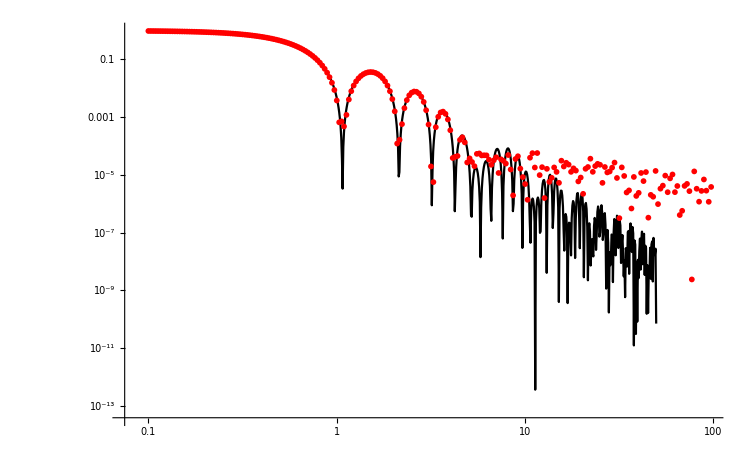

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Fshell
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="FF.q";
OFILE=DIRO1<>"FF.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Form factor amplitude (center):

-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3))

{{σR2→(q^2 Ri^4+q^2 Ri^3 Ro+q^2 Ri^2 Ro^2+q^2 Ri Ro^3+q^2 Ro^4)/(-10 q^2 Ri^2-10 q^2 Ri Ro-10 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/FFA_center.dat

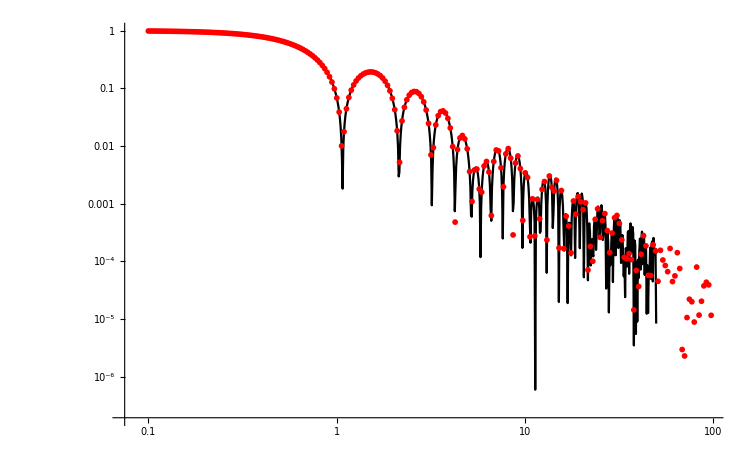

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Ashellcenter
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="FFAcenter.q";
OFILE=DIRO1<>"FFA_center.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Form factor amplitude (inner shell surface):

(Sin[q Ri] (-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3))))/(q Ri)

{{σR2→(8 q^2 Ri^4+8 q^2 Ri^3 Ro+8 q^2 Ri^2 Ro^2+3 q^2 Ri Ro^3+3 q^2 Ro^4)/(-30 q^2 Ri^2-30 q^2 Ri Ro-30 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/FFA_inner.dat

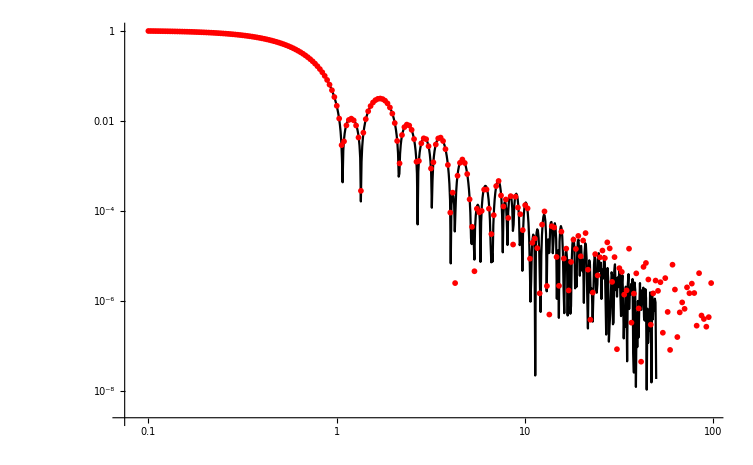

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Ainner2shell
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="FFAinner.q";
OFILE=DIRO1<>"FFA_inner.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Form factor amplitude (outer shell surface):

(Sin[q Ro] (-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3))))/(q Ro)

{{σR2→(3 q^2 Ri^4+3 q^2 Ri^3 Ro+8 q^2 Ri^2 Ro^2+8 q^2 Ri Ro^3+8 q^2 Ro^4)/(-30 q^2 Ri^2-30 q^2 Ri Ro-30 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/FFA_outer.dat

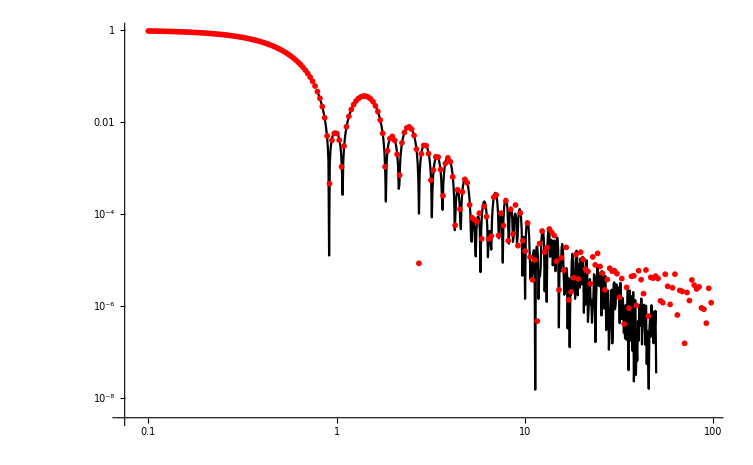

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Aouter2shell
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="FFAouter.q";
OFILE=DIRO1<>"FFA_outer.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Form factor amplitude (surface):

(((4 π Ri Sin[q Ri])/q+(4 π Ro Sin[q Ro])/q) (-(3 Ri Cos[q Ri])/(q^2 (Ri^3-Ro^3))+(3 Ro Cos[q Ro])/(q^2 (Ri^3-Ro^3))+(3 Sin[q Ri])/(q^3 (Ri^3-Ro^3))-(3 Sin[q Ro])/(q^3 (Ri^3-Ro^3))))/(4 π (Ri^2+Ro^2))

{{σR2→(8 q^2 Ri^6+8 q^2 Ri^5 Ro+11 q^2 Ri^4 Ro^2+6 q^2 Ri^3 Ro^3+11 q^2 Ri^2 Ro^4+8 q^2 Ri Ro^5+8 q^2 Ro^6)/(-30 q^2 Ri^4-30 q^2 Ri^3 Ro-60 q^2 Ri^2 Ro^2-30 q^2 Ri Ro^3-30 q^2 Ro^4)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/FFA_surface.dat

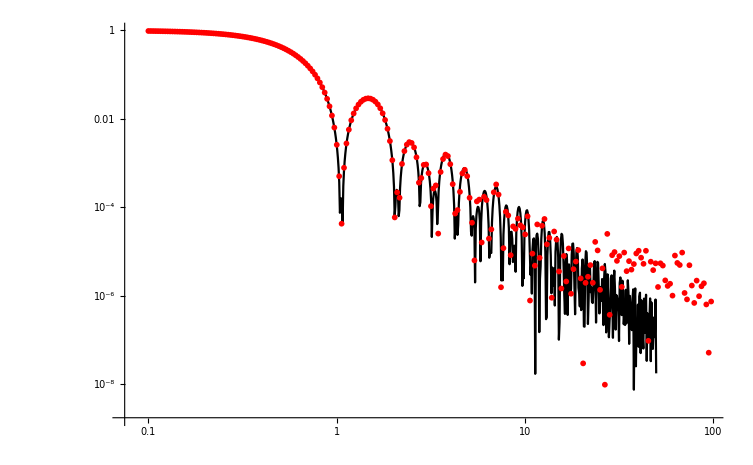

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Asurface2shell
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="FFAsurface.q";
OFILE=DIRO1<>"FFA_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (center to surface):

((4 π Ri Sin[q Ri])/q+(4 π Ro Sin[q Ro])/q)/(4 π (Ri^2+Ro^2))

{{σR2→(q^2 Ri^4+q^2 Ro^4)/(-6 q^2 Ri^2-6 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_center_surface.dat

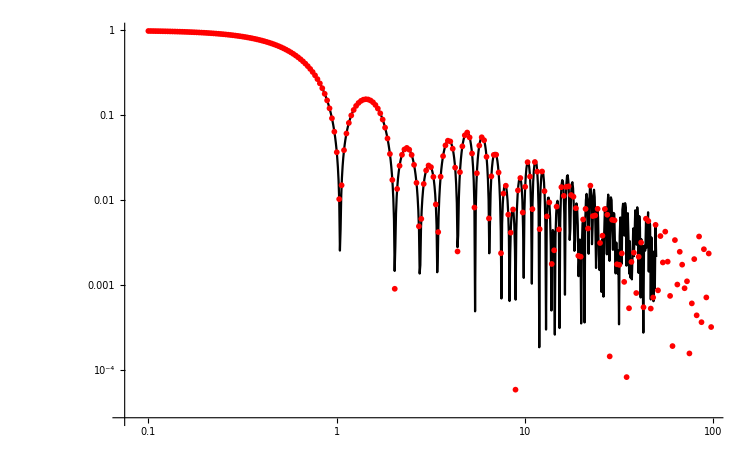

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Pcenter2surface
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Pcenter_surface.q";
OFILE=DIRO1<>"PF_center_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (inner surface to inner surface):

Sin[q Ri]^2/(q^2 Ri^2)

{{σR2→-Ri^2/3}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_inner_inner.dat

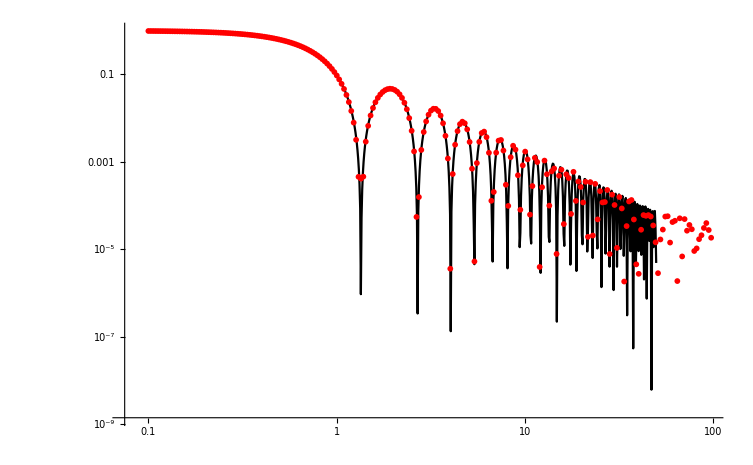

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Pinner2inner
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Pinner_inner.q";
OFILE=DIRO1<>"PF_inner_inner.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (inner surface to outer surface):

(Sin[q Ri] Sin[q Ro])/(q^2 Ri Ro)

{{σR2→-(q^2 Ri^2+q^2 Ro^2)/(6 q^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_inner_outer.dat

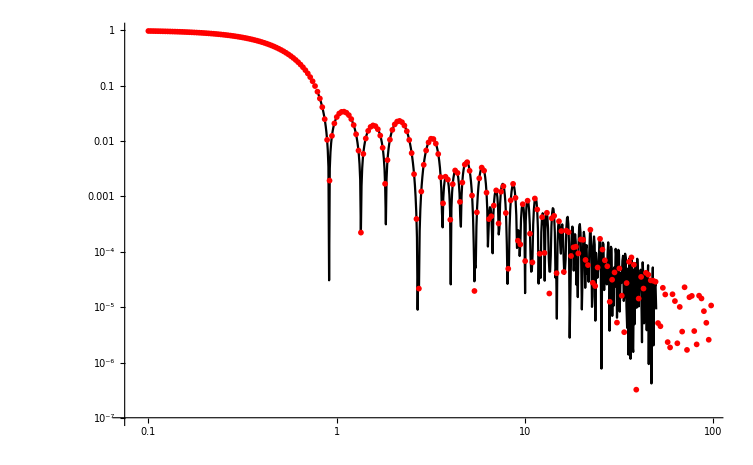

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Pinner2outer
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Pinner_outer.q";
OFILE=DIRO1<>"PF_inner_outer.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (inner surface to all surface):

(Sin[q Ri] ((4 π Ri Sin[q Ri])/q+(4 π Ro Sin[q Ro])/q))/(4 π q Ri (Ri^2+Ro^2))

{{σR2→(2 q^2 Ri^4+q^2 Ri^2 Ro^2+q^2 Ro^4)/(-6 q^2 Ri^2-6 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_inner_surface.dat

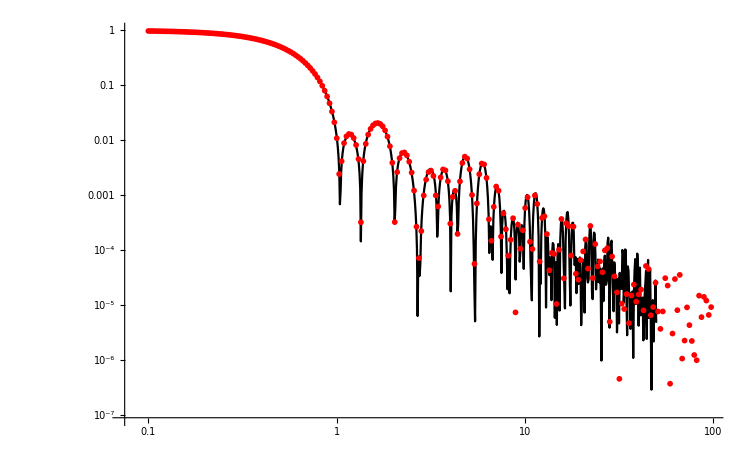

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Pinner2surface
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Pinner_surface.q";
OFILE=DIRO1<>"PF_inner_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (outer surface to outer surface):

Sin[q Ro]^2/(q^2 Ro^2)

{{σR2→-Ro^2/3}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_outer_outer.dat

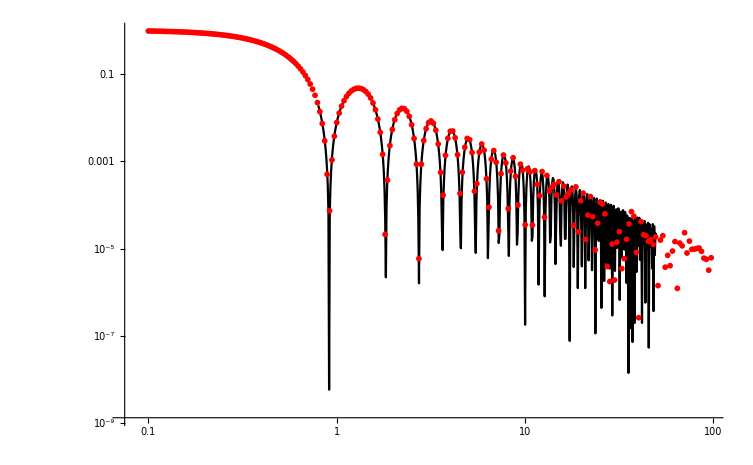

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Pouter2outer
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Pouter_outer.q";
OFILE=DIRO1<>"PF_outer_outer.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (outer surface to all surface):

(Sin[q Ro] ((4 π Ri Sin[q Ri])/q+(4 π Ro Sin[q Ro])/q))/(4 π q Ro (Ri^2+Ro^2))

{{σR2→(q^2 Ri^4+q^2 Ri^2 Ro^2+2 q^2 Ro^4)/(-6 q^2 Ri^2-6 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_outer_surface.dat

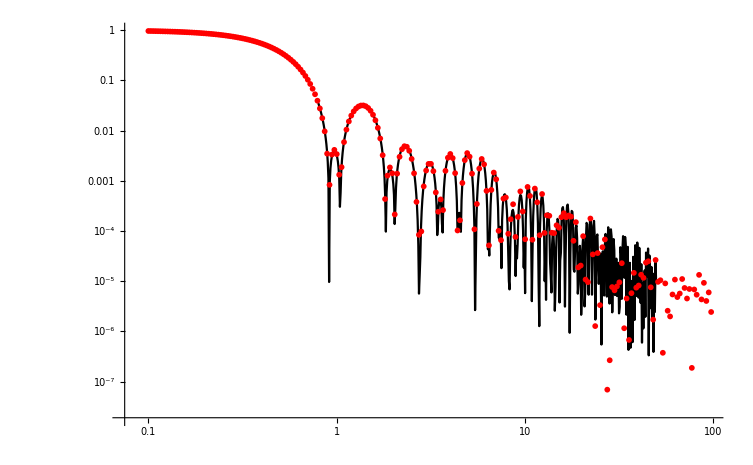

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Pouter2surface
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Pouter_surface.q";
OFILE=DIRO1<>"PF_outer_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Phase factor (all surface to all surface):

((4 π Ri Sin[q Ri])/q+(4 π Ro Sin[q Ro])/q)^2/(16 π^2 (Ri^2+Ro^2)^2)

{{σR2→(q^2 Ri^4+q^2 Ro^4)/(-3 q^2 Ri^2-3 q^2 Ro^2)}}

/home/zqex/source/SEB/Mathematica/../Examples/Validation/SolidSphericalShell_Ri2.33_Ro3.44/PF_surface_surface.dat

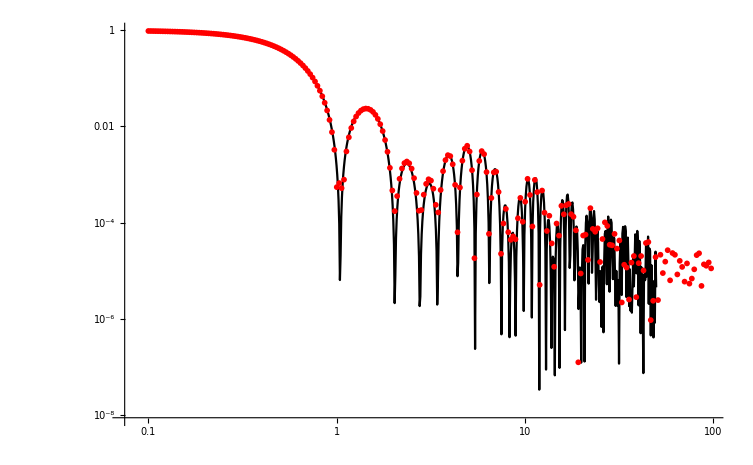

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Psurface2surface
Solve[Normal[Series[Term[q],{q,0,2}]]==1+q^2 σR2,σR2]
Func1[q_]:=Term[q]/.Ri->2.33/.Ro-> 3.44
FILE="Psurface_surface.q";
OFILE=DIRO1<>"PF_surface_surface.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```